# Calculation of DOS for Cu spd - Hamiltonian

```mathematica
Needs["GroupTheory`"];
```

a::shdw: Symbol a appears in multiple contexts {GroupTheory`Symbols`,Global`}; definitions in context GroupTheory`Symbols` may shadow or be shadowed by other definitions.

a$::shdw: Symbol a$ appears in multiple contexts {GroupTheory`Symbols`,Global`}; definitions in context GroupTheory`Symbols` may shadow or be shadowed by other definitions.

b::shdw: Symbol b appears in multiple contexts {GroupTheory`CrystalStructure`,Global`}; definitions in context GroupTheory`CrystalStructure` may shadow or be shadowed by other definitions.

b$::shdw: Symbol b$ appears in multiple contexts {GroupTheory`CrystalStructure`,Global`}; definitions in context GroupTheory`CrystalStructure` may shadow or be shadowed by other definitions.

CreateDirectory::badfile: The specified argument, GroupTheory`Auxiliary`Private`dest$29870, should be a valid string or File.

CreateDirectory::fdnfnd: Directory or file "GroupTheory`Auxiliary`Private`dest$29870" not found.

ExtractArchive::chtype2: Argument GroupTheory`Auxiliary`Private`src$29870 at position 1 is not a valid file, directory, or URL specification.

```mathematica
dir=NotebookDirectory[];
```

```mathematica
<<sim_test.wl
```

## Read ETB-Parameters and Hamiltonian

Set the directory

```mathematica
SetDirectory[dir<>"../../../math"];
```

Read the Hamiltonian

```mathematica
hfcc= GTReadFromFile["fcc_spd.ham"];
```

Read the TB parameters

```mathematica
cu=GTTbDatabaseRetrieve["TB_Handbook","Cu"];
```

```mathematica
GTTbPrintParmSet["TB_Handbook","Cu"];
```

Name       : | Cu
Structure  : | fcc
Authors    : | Papaconstantopoulos
Reference  : | Handbook of the Bandstructure of Elemental Solids, Springer, 1986

(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.07518 | 0.11571 | 0.19669 | 0.0194 | -0.03107 | -0.03289 | 0.01753 | -0.02566 | 0.018 | -0.00408

(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
-0.00092 | 0.01221 | 0.05389 | 0.00846 | -0.00852 | -0.00536 | 0.00321 | -0.00451 | 0.00241 | -0.00029

(ss0) | (pp0) | (dd0) | (dd1) | (dd2) | (pd0)
0.79466 | 1.35351 | 0.37 | 0.37307 | 0.3718 | 0.

Prepare the Hamiltonian for calculation

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu];
```

## GTPack calculation of the DOS

The DOS is calculated by means of  the Gaussian smearing method.

### Total DOS

A limited number of k points is used.  Total DOS and integrated DOS are calculated.

2304 k-points calculated

integrated DOS = 12.3334

Fermi Energy E_F= 0.569475 (units see band structure)

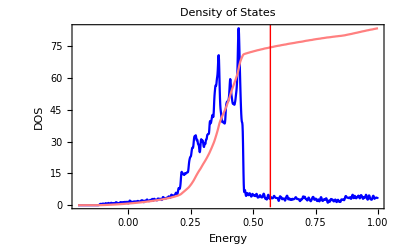

```mathematica
dosp={7,1,-0.2,1,1201,0.002,2};dos1=GTDensityOfStates[hfccp,"fcc",dosp,PlotStyle->{Blue,Pink},GOFermiEnergy->11.,GOPlotDos->"ALL"]
```

Only the total DOS is calculated.

2304 k-points calculated

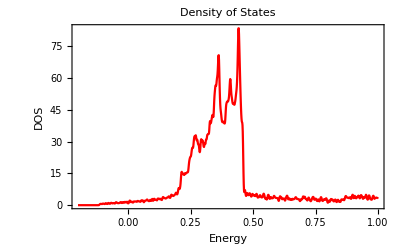

```mathematica
dosp={7,1,-0.2,1,1201,0.002,2};dos11=GTDensityOfStates[hfccp,"fcc",dosp,PlotStyle->Red,GOPlotDos->"DOS"]
```

### Partial DOS

The main components of the DOS are the partial DOSes of t_(2g) and e_g symmetry

2304 k-points calculated

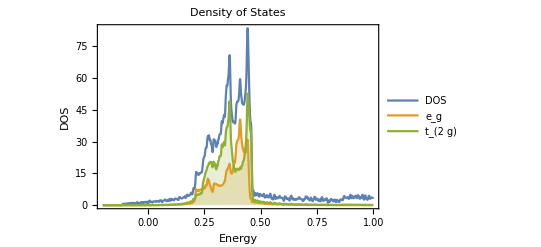

```mathematica
dosp={7,1,-.2,1.0,1201,0.002,2,{{"e_g",{7,9}},{"t_(2  g)",{5,6,8}}}};
dos2=GTPartialDOS[hfccp,"fcc",dosp,GOPlotDos->"PDOS"]
```

This calculation takes  time. Thus, doing the calculation of partial DOS with the FORTRAN code will save time.

## Calculations with SimPack

### Export data

#### Export TB parameters

```mathematica
SetDirectory[dir<>"../dos"];
```

```mathematica
GTTbParmExport[cu,"cu.parm","Cu parameters from Papaconstantopoulos"];
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.07518 | 0.11571 | 0.19669 | 0.0194 | -0.03107 | -0.03289 | 0.01753 | -0.02566 | 0.018 | -0.00408

11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
-0.00092 | 0.01221 | 0.05389 | 0.00846 | -0.00852 | -0.00536 | 0.00321 | -0.00451 | 0.00241 | -0.00029

21 | 22 | 23 | 24 | 25 | 26
(ss0) | (pp0) | (dd0) | (dd1) | (dd2) | (pd0)
0.79466 | 1.35351 | 0.37 | 0.37307 | 0.3718 | 0.

#### Export k-vectors

We take the same number of k-points

```mathematica
kpts=GTBZPointMesh[7,1,"fcc"];
```

2304 k-points calculated

export the k-vectors.

```mathematica
GTBZTbPointMesh["k2304.vec",kpts,13,5,GOOutput->"DOS"]
```

Use k-points in FORTRAN-ETBM calculation for DOS

Output in file    : k2304.vec

Number of k-points: 2304

k2304.vec

We export also a much larger number of  k-points to demonstrate that the FORTRAN calculation is much faster.

```mathematica
kpts=GTBZPointMesh[15,1,"fcc"];
```

20096 k-points calculated

```mathematica
GTBZTbPointMesh["k20096.vec",kpts,13,5,GOOutput->"DOS"]
```

Use k-points in FORTRAN-ETBM calculation for DOS

Output in file    : k20096.vec

Number of k-points: 20096

k20096.vec

### Import results from SimPack calculation

```mathematica
SetDirectory[dir<>"../dos"];
```

#### Import total DOS calculated with exported k-mesh and Gaussian smearing

emin | de  | emax |  Fermi energy E_F | electrons
-0.2 | 0.001 | 1. | 0.56935 | 11.

number of densities 2  energy points = 1210

| total
DOS | 3.3909
N_el | 10.9932

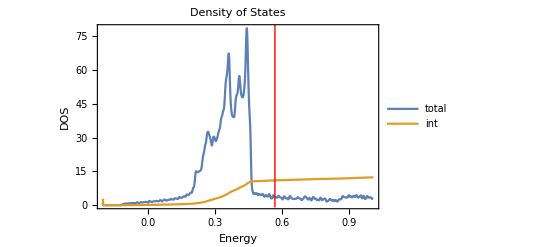

```mathematica
dosf1=GTTbReadDOS1["dg_2304.dos",{"total","int"},GOPlotDos->True]
```

Note, in Papaconstantopoulos’s “Handbook of the Band Structure of Elemental solids” the Fermi energy is  E_F= 0.5805 Ry. The deviations are due to the Hamiltonian (two-center, orthogonal) and the method of calculation. The value improves, if more   k-points tare used. Also the DOS at the Fermi energy is in better agreement with the value in the book.

#### Comparison of GTPack and SimPack calculation

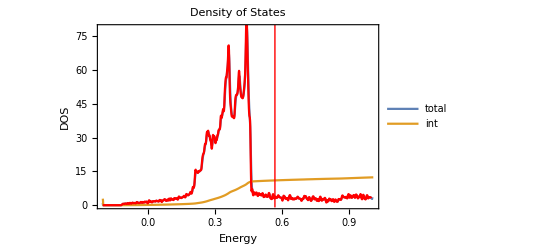

```mathematica
Show[dosf1,dos11]
```

FORTRAN calculation and GTPack calculation fit perfect.

#### Calculation of partial DOS with Gaussian smearing

For this calculation a restricted number of  k-points is used. There are deviations in Fermi energy and DOS and number of electrons in each channel compared to the book.

emin | de  | emax |  Fermi energy E_F | electrons
-0.2 | 0.001 | 1. | 0.56946 | 11.

number of densities 7  energy points = 1200

| total | s | p | t2g | eg
DOS | 3.18003 | 0.805874 | 1.50258 | 1.03792 | 0.632509
N_el | 10.9935 | 0.724614 | 0.480333 | 5.87375 | 3.94818

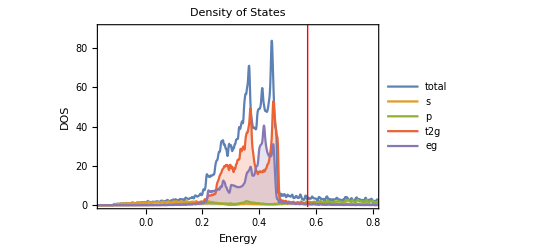

```mathematica
dosp=GTTbReadDOS1["dgp_2304.dos",{"s","p","t2g","eg"},PlotRange->{{-.15,.8},{0,90}},GOPlotDos->True]
```

#### Total DOS with Gaussian smearing and mesh from tetrahedron method

If Gaussian smearing is used, we can use also the k-mesh generated for the tetrahedron methods.

emin | de  | emax |  Fermi energy E_F | electrons
-0.2 | 0.001 | 1. | 0.56939 | 11.

number of densities 2  energy points = 1210

| total
DOS | 3.28556
N_el | 10.9934

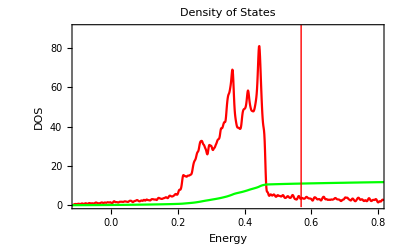

```mathematica
dosf3=GTTbReadDOS1["dtg_tetra.dos",{},GOPlotDos->True,PlotRange->{{-.1,.8},{0,90}},PlotStyle->{Red,Green}]
```

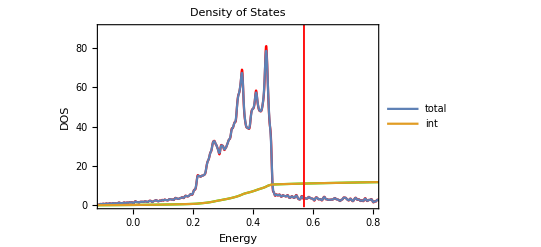

```mathematica
Show[dosf3,dosf1]
```

If Gaussian smearing is used, the different k-meshes lead to identical results!

#### Total DOS with tetrahedron method TETRA

emin | de  | emax |  Fermi energy E_F | electrons
-0.2 | 0.001 | 1. | 0.57083 | 11.

number of densities 2  energy points = 1210

| total
DOS | 3.92162
N_el | 10.9924

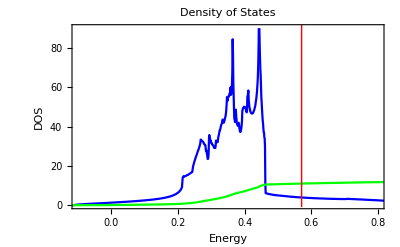

```mathematica
dost1=GTTbReadDOS1["dt_tetra.dos",{},GOPlotDos->True,PlotRange->{{-.1,.8},{0,90}},PlotStyle->{Blue,Green}]
```

#### Comparison with Gaussian smearing in GTPack

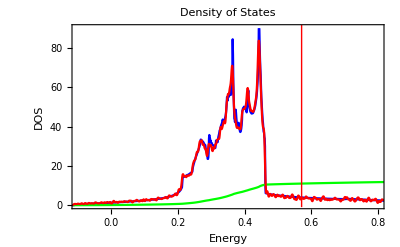

```mathematica
Show[dost1,dos11]
```

#### Partial DOS with tetrahedron method TETRA

emin | de  | emax |  Fermi energy E_F | electrons
-0.2 | 0.001 | 1. | 0.572 | 11.

number of densities 7  energy points = 1200

| total | s | p | t2g | eg
DOS | 3.9029 | 0.95504 | 1.62161 | 0.8901 | 0.50193
N_el | 10.9922 | 0.708582 | 0.495169 | 5.87117 | 3.94888

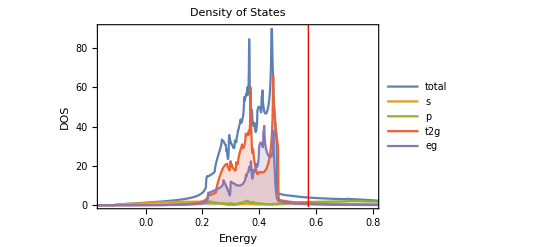

```mathematica
GTTbReadDOS1["dtp_tetra.dos",{"s","p","t2g","eg"},PlotRange->{{-.15,.8},{0,90}},GOPlotDos->True]
```